## Initialize notebook

```mathematica
Quit[];
```

```mathematica
<<Toolbox`
<<MASSef`

SetDirectory[NotebookDirectory[]];
```

## Model generation

```mathematica
fitLabel="";
mainDir="/home/mrama/Dropbox/PhD_stuff/Projects/eMASS/";
Import[mainDir<>"code/model_building_functions.m"];
Import[mainDir<>"code/enzyme_model_building.m"];
Import[mainDir<>"code/model_checks.m"];

Import[mainDir<>"enzyme_level_models-data/m_files/enzyme_models.m"];
metsData=mainDir<>"data/mets_concentrations_rabinowitz2016.xls";


metsToIgnore={h^c,h2o^c};
```

```mathematica
(* define reactions in the model *)
allReactions={str2mass["ENO: 2pg[c] <=> pep[c]"],
			str2mass["FBA1: fdp[c] <=> dhap[c] + g3p[c]"],
			str2mass["FBA2: fdp[c] <=> dhap[c] + g3p[c]"],
			str2mass["GAPD: g3p[c] + nad[c] + pi[c] <=> 13dpg[c] + nadh[c]"],
			str2mass["PGK: 13dpg[c] + adp[c] <=> 3pg[c] + atp[c]"],
			str2mass["PGMd: 3pg[c] + 23dpg[c] <=> 2pg[c] + 23dpg[c]"],
			str2mass["PGMi: 3pg[c] <=> 2pg[c]"],
			str2mass["TPI: dhap[c] <=> g3p[c]"]};

allEnzymes = {"ENO", "FBA1", "FBA2",  "GAPD", "PGK", "PGMd", "PGMi", "TPI"};

KeqList = {"ENO"-> 5.19, "FBA1"-> 0.00016, "FBA2"-> 0.00016,  "GAPD"-> 0.452,"PGK"-> 1900, "PGMd"-> 0.7, "PGMi"-> 0.98, "TPI"-> 0.107};

fluxes={Underscript[v, ENO]->  0.00011,Underscript[v, FBA1]->0.1*6.1*10^-5, Underscript[v, FBA2]->0.9*6.1*10^-5,Underscript[v, GAPD]->  0.00011,Underscript[v, PGK]-> 0.00011,Underscript[v, PGMd]-> 0.82* 0.00011 ,Underscript[v, PGMi]->0.18*  0.00011,  Underscript[v, TPI]-> 5.9*10^-5};
```

```mathematica
enzConc = {Underscript[ENO_total, Global]-> 1.88*10^-5,Underscript[FBA1_total, Global]-> 1.12*10^-6,Underscript[FBA2_total, Global]->  1.04*10^-5, Underscript[GAPD_total, Global]-> 2.44*10^-5,Underscript[PGK_total, Global]->  2.08*10^-5, Underscript[PGMd_total, Global]-> 6.26*10^-6, Underscript[PGMi_total, Global]-> 1.38*10^-6 ,Underscript[TPI_total, Global]->  3.86*10^-6};
```

```mathematica
rateConstSubList1={ENORateConstSub1, FBA1RateConstSub1, FBA2RateConstSub1,GAPDRateConstSub1, PGKRateConstSub1,PGMdRateConstSub1, PGMiRateConstSub1, TPIRateConstSub1};
rateConstSubList2={ENORateConstSub2, FBA1RateConstSub2, FBA2RateConstSub2,GAPDRateConstSub2, PGKRateConstSub2,PGMdRateConstSub2, PGMiRateConstSub2, TPIRateConstSub2};
```

```mathematica
rateConstList=Table[
Import[mainDir<>"enzyme_level_models-data/m_files/"<>enzName<>"_rateConsts.m", "MX"],
{enzName,allEnzymes}];
rateConstList=Flatten@rateConstList;
```

```mathematica
(* build model *)
enzModelsList={ENOmodel, FBA1model, FBA2model,GAPDmodel, PGKmodel,PGMdmodel, PGMimodel, TPImodel};
model = Union@@enzModelsList;
```

```mathematica
model=defineInitialConditions[model, metsData];
updateIgnore[model, metsToIgnore];
```

```mathematica
(* get enzyme form solutions *)
allEnzSol=
Table[
	Import[mainDir<>"enzyme_level_models-data/m_files/enzSol_"<>enzName<>"_.m"],
{enzName, allEnzymes}];

(* get absolute flux equations *)
allAbsFlux=
Table[
	Import[mainDir<>"enzyme_level_models-data/m_files/absoluteFlux_"<>enzName<>"_.m"],
{enzName, allEnzymes}];
```

```mathematica
(* simplify equations for enzyme form solutions *)
allEnzSol=Table[
Print[eqI];
anonymize[Simplify[allEnzSol[[eqI]], TimeConstraint->{10, 120}]],
{eqI, 1, Length@allEnzSol}];
```

1

2

3

4

5

6

7

8

```mathematica
(* simplify equations for absolute flux *)
allAbsFlux=Table[
Print[eqI];
anonymize[Simplify[allAbsFlux[[eqI]], TimeConstraint->{10, 120}]],
{eqI, 1, Length@allAbsFlux}];
```

1

2

3

4

5

6

7

8

```mathematica
(* set up met_tot and enz_tot constraints *)
modelMetabolites = Cases[model["Species"], _metabolite];

metTotalSub = Table[
	met->  parameter[getID@met<>"_total"],
{met, modelMetabolites}];

metConstraintsRule= Table[
met -> parameter[getID@met<>"_total"]-  Total@getBoundMetaboliteForms[model, met],
{met, modelMetabolites}];
```

```mathematica
metConstraintsEq =Table[

metPos = Position[StringCases[Map[getID@#&,Keys@model["InitialConditions"]], getID@met], {getID@met}];

If[Length[metPos] > 1,
metPos = Position[Map[{getID@#== getID@met<>"_total"}&,Keys@model["InitialConditions"]], {True}];
];

totMet = Keys@model["InitialConditions"][[metPos[[1]]]][[1]];
totMet == met+  Total@getBoundMetaboliteForms[model, met],

{met, modelMetabolites}];
```

```mathematica
enzymeConstraintsEq  = Table[
totEnz = parameter[enz<>"_total"];
  totEnz == Total@getEnzymeForms[model, enz],
{enz, allEnzymes}];

enzymeForms =  Table[
totEnz =  parameter[enz<>"_total"];
  getEnzymeForms[model, enz],
{enz, allEnzymes}] // Flatten;

enzymeTotList=  Table[
parameter[getID@allReactions[[i]] <> "_total"],
{i,1, Length@ allReactions}] ;
```

```mathematica
metConstraintsEq//TableForm
```

(13dpg_total)_Global==(GAPD^c&nadh^c&(13dpg)^c)_^+(PGK^c&(13dpg)^c)_^+(PGK^c&(13dpg)^c&adp^c)_^+(13dpg)^c
(2pg_total)_Global==(ENO^c&(2pg)^c)_^+(PGMd^c&(23dpg)^c&(2pg)^c)_^+(PGMi^c&(2pg)^c)_^+(2pg)^c
(3pg_total)_Global==(PGK^c&(3pg)^c)_^+(PGK^c&(3pg)^c&atp^c)_^+(PGMd^c&(23dpg)^c&(3pg)^c)_^+(PGMi^c&(3pg)^c)_^+(3pg)^c
adp_total_Global==(PGK^c&adp^c)_^+(PGK^c&(13dpg)^c&adp^c)_^+adp^c
atp_total_Global==(PGK^c&atp^c)_^+(PGK^c&(3pg)^c&atp^c)_^+atp^c
dhap_total_Global==(FBA1^c&dhap^c)_^+(FBA1^c&dhap^c&g3p^c)_^+(FBA2^c&dhap^c)_^+(FBA2^c&dhap^c&g3p^c)_^+(TPI^c&dhap^c)_^+dhap^c
fdp_total_Global==(FBA1^c&fdp^c)_^+(FBA2^c&fdp^c)_^+(FBA2^c&fdp^c&g3p^c)_^+fdp^c
g3p_total_Global==(FBA1^c&dhap^c&g3p^c)_^+(FBA2^c&g3p^c)_^+(FBA2^c&dhap^c&g3p^c)_^+(FBA2^c&fdp^c&g3p^c)_^+(GAPD^c&nad^c&g3p^c)_^+(GAPD^c&nad^c&g3p^c&pi^c)_^+(TPI^c&g3p^c)_^+g3p^c
nad_total_Global==(GAPD^c&nad^c)_^+(GAPD^c&nad^c&g3p^c)_^+(GAPD^c&nad^c&g3p^c&pi^c)_^+nad^c
nadh_total_Global==(GAPD^c&nadh^c)_^+(GAPD^c&nadh^c&(13dpg)^c)_^+nadh^c
pep_total_Global==(ENO^c&pep^c)_^+pep^c
pi_total_Global==(GAPD^c&nad^c&g3p^c&pi^c)_^+pi^c
(23dpg_total)_Global==(PGMd^c&(23dpg)^c)_^+(PGMd^c&(23dpg)^c&(2pg)^c)_^+(PGMd^c&(23dpg)^c&(3pg)^c)_^+(23dpg)^c

### Solve enzyme forms to get E_i = f(E_tot, x_free) Calculate FBA flux to get v_ss ( setting it to 1) Create the steady state flux equations by summing the catalytic track rate laws and subbing in E_i to get v_ss = f(E_tot, x_free) Combine two sets of equations x_total = x_free + sum (E_i_x) (sub in E_i_x from the first step) This yields x_total = x_free + sum(f(E_tot,x_free)) v_ss = f(E_tot, x_free) Solve the system of equations for E_tot and x_free simultaneously

#### Define functions

```mathematica
ToPythonCustom1[x_] := StringReplace[ToString[x,InputForm], {
			"\""-> "","["->"(","]"->")","<"->"[",">"->"]",(*" "->"",*)"Sqrt"->"sqrt","Log"->"log","List"->"list","*^"->"e","^"->"**", "{"-> "[", "}"-> "]"}];

ToPythonCustom2[x_] := StringReplace[ToString[x,InputForm], {
			"["->"(","]"->")","<"->"[",">"->"]",(*" "->"",*)"Sqrt"->"sqrt","Log"->"log","List"->"list","*^"->"e","^"->"e", "{"-> "[", "}"-> "]"}];



getRateConstantsSub[mainDir_, rateConstIndList_, allEnzymes_, rateConstList_,rateConstSubList1_, rateConstSubList2_]:=Block[{allRateConstValues,   rateConstValuesSub},
(* import rate constant values *)

allRateConstValues = Table[
	Import[mainDir<>"enzyme_level_models-data/results/rateconst_"<>allEnzymes[[enzNameI]]<>"_.csv", "TSV"][[rateConstIndList[[enzNameI]],2;;]],
{enzNameI, 1, Length@allEnzymes}];
allRateConstValues=Flatten@allRateConstValues;

(*allRateConsts=DeleteDuplicates[Flatten@DeleteDuplicates[Map[Reverse@DeleteDuplicates[Cases[#, _rateconst,∞]]&,keq2kHT@model["Rates"]]]/.Flatten@rateConstSubList1/.Flatten@rateConstSubList2];
allRateConsts=Table[
		DeleteDuplicates[Flatten[Map[{rateconst[getID[#],False],rateconst[getID[#],True]}& , enzModelsList[[enzI]]["Reactions"]]]/.rateConstSubList1[[enzI]]/.rateConstSubList2[[enzI]]],
	{enzI, 1, Length@enzModels}];*)

rateConstValuesSub= Thread[ rateConstList->  allRateConstValues];

Return[rateConstValuesSub];
];


convertEqsToPythonWithFluxMetTotValues[eqSystem_,vars_, fluxIDs_] :=Block[{varSub,eqVals={}, eqsOnly={}, allVars,eqSystemRHS,eqSystemLHS,fluxVars, eq},

varSub = Thread[vars -> Map[getID[#]&, vars]];
Do[
Print[eqI];
eq=eqSystem[[eqI]];
If[NumberQ[eq[[1]]],

AppendTo[eqVals, eq[[1]]];
AppendTo[eqsOnly,anonymize[Simplify[eq[[2]], TimeConstraint->{10,120}]]];,

AppendTo[eqVals,anonymize[Simplify[eq[[2]], TimeConstraint->{10,120}]]];
AppendTo[eqsOnly, eq[[1]]];
];,

{eqI, 1, Length@eqSystem}];

(*eqVals = eqSystem[[All,1]];
eqsOnly =eqSystem[[All,2]];*)


eqsOnly = eqsOnly/.varSub;
eqsOnly =ToPythonCustom1[eqsOnly];
eqVals = ToPythonCustom2[eqVals];
allVars =ToPythonCustom2[Values@varSub];
fluxVars = ToPythonCustom2[fluxIDs];

Return[{eqsOnly, eqVals, allVars, fluxVars}];
];


exportEqsWithFluxMetTotValues[eqSystem_, eqVals_, vars_, fluxIDs_, filePath_]:=Block[{},

Export[filePath<>"_eqs.txt", eqSystem];
Export[filePath<>"_eq_vals.txt", eqVals];
Export[filePath<> "_varIDs.txt", vars];
Export[filePath<> "_fluxIDs.txt", fluxIDs];

];

selectRateConstantSets[nEnzymes_, nFirstSets_, nRateConstSets_]:=Block[{rateConstSets},

rateConstSets = 
	Table[
		Table[
			RandomInteger[{1,nFirstSets}], 
		{i, 1,nEnzymes}],
	{j, 1, nRateConstSets}];

Return[rateConstSets];

];
```

#### Select rate constants sets to be used

```mathematica
rateConstSets=Tuples[Range[3],{8}];
Length@rateConstSets
```

6561

#### Set up flux equations

```mathematica
volumeSub=Underscript[Volume, c]->1;
metSubForPython ={(13dpg)^c->m["dpg","c"] , (3pg)^c-> m["threepg","c"], (2pg)^c-> m["twopg","c"], (23dpg)^c-> m["two3pg","c"]};
```

```mathematica
fluxIDs=Map[StringRiffle[getID@#,""]&,Keys@fluxes];
fluxEqs = Map[Keys@#== Values@#&,allAbsFlux];
vars=Flatten@{Map[#[[1]]&,enzymeConstraintsEq],modelMetabolites};
```

```mathematica
enzSol=Flatten@allEnzSol;
posConstraint=Map[#≥ 0.&, vars];
eqSystemGeneral =Flatten@{fluxEqs,metConstraintsEq}/.enzSol/.fluxes/.stripUnits@model["InitialConditions"];
```

```mathematica
rateConstsSubPython=Thread[rateConstList -> Table["x<"<>ToString[i]<>">", {i,0,Length[rateConstList]-1}]];
```

#### Export flux equations

```mathematica
eqSystemSubbed= eqSystemGeneral/.volumeSub/.metSubForPython/.rateConstsSubPython;
varsSubbed = vars/.metSubForPython;
```

```mathematica
{eqSystemConverted, eqVals, varsConverted, fluxIDsConverted}=convertEqsToPythonWithFluxMetTotValues[eqSystemSubbed, varsSubbed,fluxIDs];
```

1

2

3

4

5

6

7

8

9

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

10

11

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

12

13

14

15

16

17

18

19

20

21

```mathematica
CreateDirectory[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel]
```

/home/mrama/Dropbox/PhD_stuff/Projects/eMASS/eMASSpy/data_8enz

```mathematica
exportEqsWithFluxMetTotValues[eqSystemConverted, eqVals, varsConverted,fluxIDsConverted, mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/data"];
```

#### Export rate constants

```mathematica
rateConsts = 
Table[
	Print[rateConstSetI];
	Values@getRateConstantsSub[mainDir, rateConstSets[[rateConstSetI]], allEnzymes,  rateConstList, rateConstSubList1, rateConstSubList2](*/.rateConstsSubPython*),
{rateConstSetI,1,Length@rateConstSets}];

Export[ mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/data_rateValues.txt",rateConsts, "CSV"];
Export[ mainDir<> "eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/data_rateSets.txt",rateConstSets, "CSV"];
```

## Model building

#### Plug-in concentrations from python

```mathematica
importFilesInRange[fileName_, startFile_, endFile_]:=Block[{mergedFiles},

mergedFiles=Table[
Import[fileName <> ToString[i] <> ".csv"][[2;;,All]],
{i, startFile, endFile}	
];
mergedFiles=Flatten[mergedFiles,1];
Return[mergedFiles];
];
```

```mathematica
lmaResults =importFilesInRange[mainDir<>"eMASSpy/cluster_results/results_8enz/lma_residual_relative_",1, 122];
```

```mathematica
lmaParamaters=importFilesInRange[mainDir<>"eMASSpy/cluster_results/results_8enz/lma_result_params_",1, 122];
```

```mathematica
lmaPrediction=importFilesInRange[mainDir<>"eMASSpy/cluster_results/results_8enz/lma_prediction_",1, 122];
```

```mathematica
threshold = 0.1;
indList01 = Flatten@Position[Map[AllTrue[#, #<threshold&]&,lmaResults[[All,3;;]]], True];
```

```mathematica
modelInd01=lmaResults[[indList01,1]]//DeleteDuplicates;
```

```mathematica
buildModelList[model_, rateConstSets_, paramSets_, lmaParamaters_, allEnzSol_, allEnzymes_, vars_, rateConstList_, rateConstSubList1_, rateConstSubList2_, mainDir_]:=Block[{modelList, modelTemp,rateConsts, initCond,enzForms,enzSol},

enzSol=Flatten@allEnzSol;

modelList=Table[
Print[i];

modelTemp=model;

If[i==5||i==Length@paramSets,
Print[rateConstSets[[paramSets[[i]]+1]]];
Print[{vars,lmaParamaters[[paramSets[[i]]+1]]}];
];

rateConsts = getRateConstantsSub[mainDir,rateConstSets[[paramSets[[i]]+1]], allEnzymes, rateConstList, rateConstSubList1, rateConstSubList2];
updateParameters[modelTemp, rateConsts];

initCond =  MapThread[#1-> #2 Mole Liter^-1&,{vars,lmaParamaters[[paramSets[[i]]+1]]}];
updateInitialConditions[modelTemp,initCond];

enzForms =enzSol/.modelTemp["Parameters"]/.stripUnits@modelTemp["InitialConditions"];
enzForms = Map[Keys@#-> Values@# Mole Liter^-1&,enzForms];
updateInitialConditions[modelTemp,enzForms];

modelTemp,

{i, 1, Length@paramSets}];

Return[modelList]];
```

#### Build and export models

```mathematica
modelList=buildModelList[model,rateConstSets, modelInd01, DeleteDuplicates[lmaParamaters[[All,3;;]]], allEnzSol, allEnzymes, vars, rateConstList, rateConstSubList1, rateConstSubList2, mainDir];

Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/modelList.m", modelList, "MX"];
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/good_models_ind_list.m",modelInd01, "MX"];
```

#### Import models

```mathematica
modelList=Import[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/modelList.m",  "MX"];
```

#### Get models with different initial ATP concentrations

```mathematica
atpConc=Flatten@Values@stripUnits@Map[FilterRules[#["InitialConditions"], atp^c]&, modelList];

atpAbove0095=Table[
If[atpConc[[entryI]]>0.0095,
entryI,
{}],
{entryI, 1, Length@modelList}];
atpAbove0095 = DeleteCases[atpAbove0095, {}];


atpBelow007=Table[
If[atpConc[[entryI]]<0.0070,
entryI,
{}],
{entryI, 1, Length@modelList}];
atpBelow007 = DeleteCases[atpBelow007, {}];


atpBetween=Table[
If[0.0077<atpConc[[entryI]]<0.0083,
entryI,
{}],
{entryI, 1, Length@modelList}];
atpBetween = DeleteCases[atpBetween, {}];
```

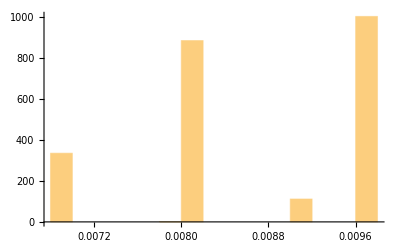

```mathematica
Histogram[atpConc]
```

#### Select subsets of models with low/high and in between ATP concentrations

```mathematica
atpBelow007Subset={159,276,72,320,243,281,52,169,4,181,266,68,226,10,55,144,119,255,277,51,81,249,330,156,224,205,328,17,110,192,296,190,87,292,66,145,132,80,123,295,233,203,275,228,40,24,331,290,312,133};(*atpBelow007Subset=RandomSample[Range[1, Length@atpBelow007], 50]*)
```

```mathematica
atpAbove0095Subset={891,516,854,448,690,754,569,628,64,428,102,146,581,282,675,724,145,228,755,199,244,486,584,946,658,546,712,887,268,404,687,141,70,915,12,85,520,543,324,392,313,636,195,851,834,406,651,376,646,723};
(*atpAbove0095Subset=RandomSample[Range[1, Length@atpAbove0095], 50]*)
```

```mathematica
atpBetweenSubset={384,508,127,860,269,814,483,198,379,723,631,293,803,750,365,43,649,801,203,438,307,380,746,186,722,226,526,383,686,27,410,264,462,14,844,56,105,615,748,370,435,760,86,302,625,112,237,881,212,735};
(*atpBetweenSubset=RandomSample[Range[1, Length@atpBetween], 50]*)
```

#### Export subsets of models with low/high and in between ATP concentrations

```mathematica
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/atpBelow007_subset.m", atpBelow007[[atpBelow007Subset]], "MX"];
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/atpAbove0095_subset.m", atpAbove0095[[atpAbove0095Subset]], "MX"];
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/atpBetween_subset.m", atpBetween[[atpBetweenSubset]], "MX"];
```

## Model simulation

```mathematica
metList=Cases[modelList[[1]]["Species"],_metabolite,Infinity]
```

{(13dpg)^c,(2pg)^c,(3pg)^c,adp^c,atp^c,dhap^c,fdp^c,g3p^c,nad^c,nadh^c,pep^c,pi^c,(23dpg)^c}

#### Simulate model

```mathematica
simulateResAtpBelow007 = Table[
simulate[modelList[[entryI]], {t,0,500}],

{entryI, atpBelow007}];
```

```mathematica
simulateResAtpAbove0095 = Table[
simulate[modelList[[entryI]], {t,0,500}],

{entryI, atpAbove0095}];
```

```mathematica
simulateResAtpBetween = Table[
simulate[modelList[[entryI]], {t,0,500}],

{entryI, atpBetween[[atpBetweenSubset]]}];
```

#### Plot simulations

```mathematica
concPlotListAtpBelow007 =Table[
plotSimulation[FilterRules[simulateResAtpBelow007[[i,1]], metList], PlotFunction->LogPlot],
{i, 1, Length@atpBelow007}];
```

```mathematica
concPlotListAtpAbove0095 =Table[
plotSimulation[FilterRules[simulateResAtpAbove0095[[i,1]], metList], PlotFunction->LogPlot],
{i, 1, Length@atpAbove0095}];
```

```mathematica
concPlotListAtpBetween=Table[
plotSimulation[FilterRules[simulateResAtpBetween[[i,1]], metList], PlotFunction->LogPlot],
{i, 1, 50}];
```

```mathematica
fluxPlotListAtpAbove0095 =Table[
plotSimulation[simulateResAtpAbove0095[[i,2]], PlotFunction->LogPlot],
{i, 1, Length@atpAbove0095}];
```

```mathematica
Show[fluxPlotListAtpAbove0095,PlotRange-> {{0,100},Automatic}]
```

```mathematica
Show[fluxPlotListAtpAbove0095,PlotRange-> {{0,500},Automatic}]
```

```mathematica
Show[concPlotListAtpBelow007, PlotRange-> {{0,100},Automatic}]
```

-Graphics-

```mathematica
Show[concPlotListAtpAbove0095, PlotRange-> {{0,100},Automatic}]
```

-Graphics-

```mathematica
Show[concPlotListAtpBetween, PlotRange-> {{0,100},Automatic}]
```

-Graphics-

#### Save simulation data

```mathematica
indEnz=Map[Position[Keys@simulateResAtpBelow007[[2,1]],#]&,Cases[modelList[[1]]["Species"],_enzyme, Infinity]]//Flatten;
indMet=Map[Position[Keys@simulateResAtpBelow007[[2,1]],#]&,Cases[modelList[[1]]["Species"],_metabolite, Infinity]]//Flatten;
```

```mathematica
headerConcEnz=Keys@simulateResAtpBelow007[[2,1]][[indEnz]];
enzNames = Map[getID@#&,headerConcEnz];
boundMets = Map[getCatalytic[#]&,headerConcEnz];
headerConcEnz=Table[
StringRiffle[Flatten@{enzNames[[i]],Map[getID@#&,boundMets[[i]]]}, "_"],
{i, 1, Length@boundMets}];
```

```mathematica
headerConcMets=Map[getID@#&,Keys@simulateResAtpBelow007[[2,1]][[indMet]]];
```

```mathematica
headerFlux=Map[getID[#]&,Keys@simulateResAtpBelow007[[2,2]]];
```

```mathematica
tValues=Map[10^#&,Range[-6,2, 0.1]];
tFinal=500;
tValues=Insert[tValues,0., 1];
```

```mathematica
Length@tValues
```

82

```mathematica
outputDir=mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel;
```

```mathematica
Import[mainDir<>"code/simulation.m"];
```

```mathematica
modelID="simulateResAtpBelow007";
getSimulationData[simulateResAtpBelow007, outputDir,  modelID, tFinal, tValues, 
				 headerConcEnz, headerConcMets, headerFlux, indEnz, indMet];
```

```mathematica
modelID="simulateResAtpAbove0095";
getSimulationData[simulateResAtpAbove0095, outputDir,  modelID, tFinal, tValues, 
				 headerConcEnz, headerConcMets, headerFlux, indEnz, indMet];
```

```mathematica
modelID="simulateResAtpBetween";
getSimulationData[simulateResAtpBetween, outputDir,  modelID, tFinal, tValues, 
				 headerConcEnz, headerConcMets, headerFlux, indEnz, indMet];
```

## Model analysis

### Calculate Jacobian

```mathematica
eigenvaluesList = Table[

jacobian=getJacobian[modelList[[ind]]]/.stripUnits[modelList[[ind]]["InitialConditions"]]/.stripUnits[modelList[[ind]]["Parameters"]];
Eigenvalues[jacobian],
{ind, 1, Length@modelList}];
```

```mathematica
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/eigenvalues_list.csv", eigenvaluesList, "CSV"];
```

```mathematica
header = Map[getID[#]&,modelList[[1]]["Species"]];
```

```mathematica
stableModelsIndListNoIM= Flatten@Position[Map[AllTrue[#, Internal`RealValuedNumericQ]&,eigenvaluesList], True]
```

{34,311,680}

```mathematica
eigenvaluesMax = Map[{Max@#[[1]],Max@#[[2]]}&,Map[{Re[#], Im[#]}&,eigenvaluesList]];
```

```mathematica
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/eigenvalues_max.csv", eigenvaluesMax, "CSV"];
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/eigenvalues_max_re.csv", eigenvaluesMax[[All,1]], "CSV"];
Export[mainDir<>"eMASSpy/data_"<>ToString[Length@allEnzymes]<>"enz"<>fitLabel<>"/eigenvalues_max_im.csv", eigenvaluesMax[[All,2]], "CSV"];
```

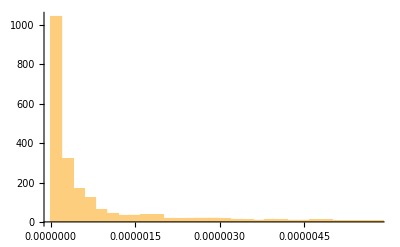

```mathematica
Histogram[eigenvaluesMax[[All,1]]]
```

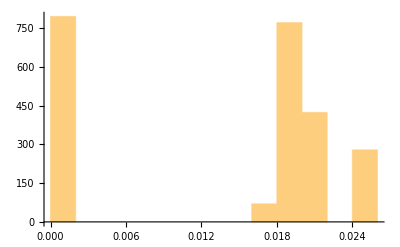

```mathematica
Histogram[eigenvaluesMax[[All,2]]]
```